```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210421_OR_model_and_other_lines_sliding"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package-2.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
datafull=Import["../data/ccm_manipulated_347418.csv"];
```

Data with Sliding Time Windows

```mathematica
x1=Round@Ceiling[Length@datafull/10,1];
{a,b,c,d,e,f,g,h,i,j}=Join[Range[x1,Length@datafull,x1],{Length@datafull}];
data1=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x1/2,z[[2]]-x1/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j},2,1]}],1]];
win1=Length@data1;
```

```mathematica
step1=11;
step2=11;
AbsoluteTiming[widthdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,9,step1,win1];]
```

{107.245,Null}

```mathematica
graphsandnodenumbers1=Table[snetworkgraph[widthdataintimewindowsFixedstep1[[1]][[i]],widthdataintimewindowsFixedstep1[[2]][[i]],2,7,400,Green],{i,Range@win1}];
```

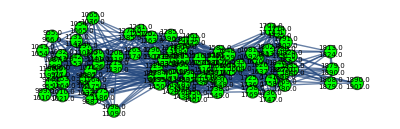

```mathematica
graphsandnodenumbers1[[4,1]]
```

```mathematica
randomizinggraphdegfxd[graphsandnodenumbers1[[4,1]]]
randomizinggraphmod[graphsandnodenumbers1[[4,1]]]
zscorefunctionfortwonullmodels[graphsandnodenumbers1[[4,1]]]
```

-Graphics-

-Graphics-

{33.797,-3.01061}

```mathematica
step1=1;
step2=1;
AbsoluteTiming[thicknessdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,10,step1,win1];]
```

{21.8442,Null}

```mathematica
graphsandnodenumbers2=Table[snetworkgraph[thicknessdataintimewindowsFixedstep1[[1]][[i]],thicknessdataintimewindowsFixedstep1[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win1}];
```

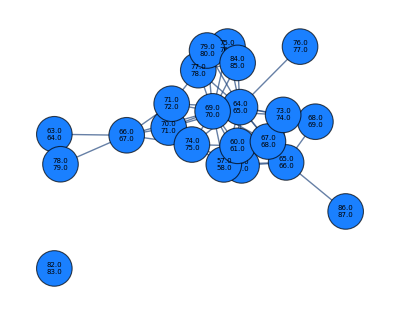

```mathematica
graphsandnodenumbers2[[13,1]]
```

```mathematica
randomizinggraphdegfxd[graphsandnodenumbers2[[13,1]]]
randomizinggraphmod[graphsandnodenumbers2[[13,1]]]
zscorefunctionfortwonullmodels[graphsandnodenumbers2[[13,1]]]
```

-Graphics-

-Graphics-

{1.884,-0.439538}